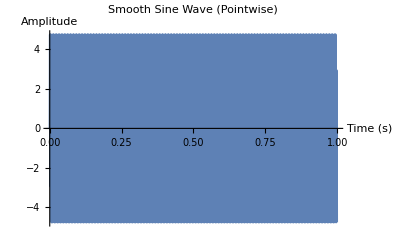

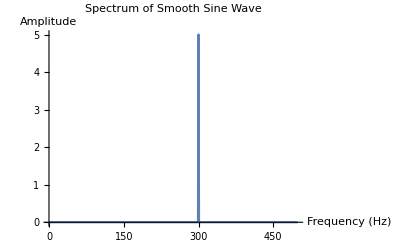

```mathematica
amplitude=5;
frequencyHz=300;(*Изменено на 300 Hz для появления пика на этой частоте*)durationSec=1;
sampleRate=1000;
t=Range[0,durationSec-1/sampleRate,1/sampleRate];
dataPoints=amplitude*Sin[2*Pi*frequencyHz*t];
n=Length[dataPoints];

(*Построение графика исходного массива точек*)
ListLinePlot[Transpose[{t,dataPoints}],PlotRange->All,AxesLabel->{"Time (s)","Amplitude"},PlotLabel->"Smooth Sine Wave (Pointwise)"]

(*Выполнение дискретного преобразования Фурье*)
fourier=Fourier[dataPoints,FourierParameters->{1,-1}];

(*Определение частотной сетки*)
freqs=Range[0,n-1]*(sampleRate/n);

(*Масштабирование амплитуды для корректного отображения*)
scaledAmplitude=2*Abs[fourier]/n;

(*Оставляем только первую половину спектра (до Nyquist'овой частоты)*)
halfLength=Floor[n/2];
freqsHalf=Take[freqs,halfLength];
amplitudeHalf=Take[scaledAmplitude,halfLength];

(*Построение спектра*)
ListLinePlot[Transpose[{freqsHalf,amplitudeHalf}],PlotRange->All,AxesLabel->{"Frequency (Hz)","Amplitude"},PlotLabel->"Spectrum of Smooth Sine Wave"]
```